```mathematica
Question 10
```

Hubble constant,  derivatives, plots and equations:

70

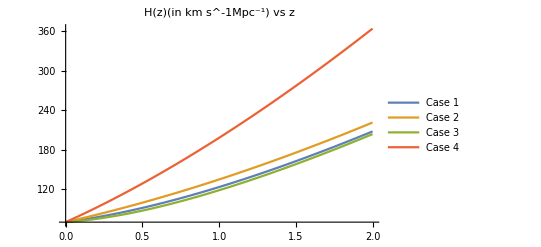

```mathematica
H0=70

Plot[{H0(0.7+ 0.3(1+x)^3)^0.5,H0(0.7 (1 + x)^0.9+ 0.3(1+x)^3)^0.5,H0(0.7 (1 + x)^-0.6+ 0.3(1+x)^3)^0.5,H0(1 + x)^(3/2)},{x,0,2},PlotLegends->{"Case 1","Case 2","Case 3","Case 4"},PlotLabel->"H(z)(in km s^-1Mpc^-1) vs z"]
```

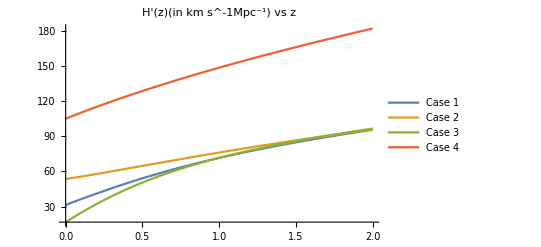

```mathematica
Plot[{Evaluate[D[H0(0.7+ 0.3(1+x)^3)^0.5,x]],Evaluate[D[H0(0.7 (1 + x)^0.9+ 0.3(1+x)^3)^0.5,x]],Evaluate[D[H0(0.7 (1 + x)^-0.6+ 0.3(1+x)^3)^0.5,x]],Evaluate[D[H0(1 + x)^(3/2),x]]},{x,0,2},PlotLegends->{"Case 1","Case 2","Case 3","Case 4"},PlotLabel->"H'(z)(in km s^-1Mpc^-1) vs z"]
```

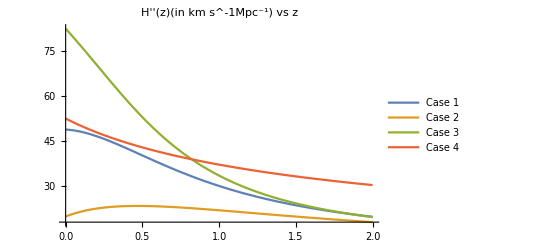

```mathematica
Plot[{Evaluate[D[H0(0.7+ 0.3(1+x)^3)^0.5,{x,2}]],Evaluate[D[H0(0.7 (1 + x)^0.9+ 0.3(1+x)^3)^0.5,{x,2}]],Evaluate[D[H0(0.7 (1 + x)^-0.6+ 0.3(1+x)^3)^0.5,{x,2}]],Evaluate[D[H0(1 + x)^(3/2),{x,2}]]},{x,0,2},PlotLegends->{"Case 1","Case 2","Case 3","Case 4"},PlotLabel->"H''(z)(in km s^-1Mpc^-1) vs z"]
```

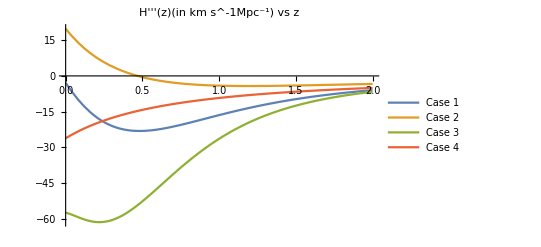

```mathematica
Plot[{Evaluate[D[H0(0.7+ 0.3(1+x)^3)^0.5,{x,3}]],Evaluate[D[H0(0.7 (1 + x)^0.9+ 0.3(1+x)^3)^0.5,{x,3}]],Evaluate[D[H0(0.7 (1 + x)^-0.6+ 0.3(1+x)^3)^0.5,{x,3}]],Evaluate[D[H0 (1 + x)^(3/2),{x,3}]]},{x,0,2},PlotLegends->{"Case 1","Case 2","Case 3","Case 4"},PlotLabel->"H'''(z)(in km s^-1Mpc^-1) vs z"]
```